```mathematica
LibraryUnload[libhello]
```

```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=BlockMap[#[[1]]->#[[2]]&,pclist,2,1];
```

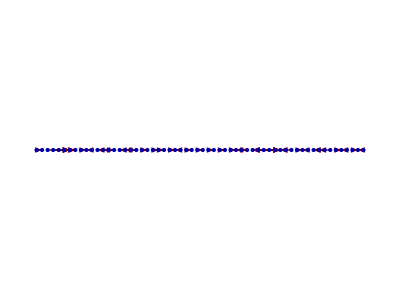

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>100&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

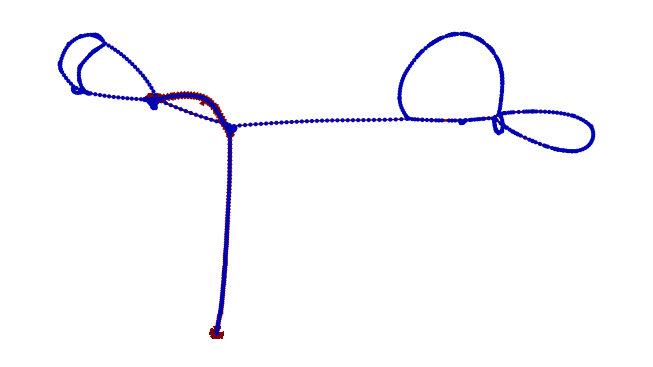

```mathematica
GraphPlot[g[[2000;;9000]],DirectedEdges-> True]
```

```mathematica
Dataset[Table[{i,BaseForm[getregister[i],16],BaseForm[getregister[i],2]},{i,1,31}]]
```

Dataset[<>]

```mathematica
regs=Table[{i,getregister[i]},{i,1,31}];
```

```mathematica
Map[#[[2]]&,regs]
```

{2768,65344,13600,0,-1,1498564676,-1,3,12288,0,67,11648,1230132307,66,66,1380982853,1313821779,12288,500,67,9996,12288,12288,12288,11636,12288,9964,2,0,1095911247,1380982853}

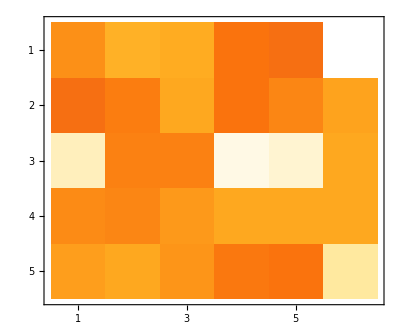

```mathematica
MatrixPlot[BlockMap[#&,Map[#[[2]]&,regs],6],ColorFunction->"SunsetColors"]
```